Red Blood Bodies: BinarizeSelector:=0.671; SmallBodiesSizeSelector:=10px;MarkerSelector:= 0.02; GradientFilterSelector:=3;

```mathematica
ClearAll["Global'*"]
rbg=-Graphics-;
(*rbg=ImageCrop[rbg,{300,340}];*)
Manipulate[{b=FillingTransform[ColorNegate[Binarize[rbg,BinarizeSelector]]],
rbc=b;
(*b=DeleteSmallComponents[rbc,SmallBodiesSizeSelector]*)
distT=DistanceTransform[b,Padding->0];
marker=MaxDetect[ImageAdjust[distT],MarkerSelector];
w=WatershedComponents[GradientFilter[b,GradientFilterSelector],marker,Method->"Rainfall"];
Colorize[w],  
cells=SelectComponents[w,"Count",SmallBodiesSizeSelector<#<BigBodiesSizeSelector&];
measures=ComponentMeasurements[cells,{"Centroid","EquivalentDiskRadius","Label"}];
Show[rbc,rbg,Graphics[{Red,Thickness[0.01], Circle@@#&/@(measures[[All,2,1;;2]]),MapThread[Text[Style[#1,16],#2+{0.0(*Shift of Circle Labels*),0.0}]&,{measures[[All,2,3]],measures[[All,2,1]]}]}]],
measures//Length
},Column[{Row[{Control[{BinarizeSelector,0,1,.001}],Control[{SmallBodiesSizeSelector,1,500,10}],Control[{BigBodiesSizeSelector,300,50000,50}]}],

Row[{Control[{MarkerSelector,0.0001,1,.001}],Control[{GradientFilterSelector,.1,10,.02}]}]

  }] ]
```

```mathematica
ClearAll["Global'*"]
rbc=-Graphics-;

b=FillingTransform[ColorNegate[Binarize[rbc]]]
distT=DistanceTransform[b,Padding->0];
marker=MaxDetect[ImageAdjust[distT],0.1];
w=WatershedComponents[GradientFilter[b,3],marker,Method->"Rainfall"];
rb=Binarize[Colorize[w]]
rbc=ImageCrop[rb,{300,340}]; rbc=rb;
b=DeleteSmallComponents[ColorNegate[Binarize[rbc,.81]],50];
distT=DistanceTransform[b,Padding->0];
marker=MaxDetect[ImageAdjust[distT],0.02];
w=WatershedComponents[GradientFilter[b,3],marker,Method->"Rainfall"];
Colorize[w]
cells=SelectComponents[w,"Count",100<#<3000&];
measures=ComponentMeasurements[cells,{"Centroid","EquivalentDiskRadius","Label"}];
Show[rbc,Graphics[{Red,Thickness[0.01], Circle@@#&/@(measures[[All,2,1;;2]]),MapThread[Text,{measures[[All,2,3]],measures[[All,2,1]]}]}]]
measures//Length
ComponentMeasurements[m,"Properties"]
```

52

{AdjacentBorderCount,AdjacentBorders,Area,AreaRadiusCoverage,AuthalicRadius,BoundingBox,BoundingBoxArea,BoundingDiskCenter,BoundingDiskCoverage,BoundingDiskRadius,CaliperElongation,CaliperLength,CaliperWidth,Centroid,Circularity,Complexity,ConvexArea,ConvexCount,ConvexCoverage,ConvexPerimeterLength,ConvexVertices,Count,Dimensions,Eccentricity,Elongation,EmbeddedComponentCount,EmbeddedComponents,EnclosingComponentCount,EnclosingComponents,EquivalentDiskRadius,EulerNumber,ExteriorNeighborCount,ExteriorNeighbors,FilledCircularity,FilledCount,Fragmentation,Holes,InteriorNeighborCount,InteriorNeighbors,Label,LabelCount,Length,Mask,MaxCentroidDistance,MaxPerimeterDistance,MeanCaliperDiameter,MeanCentroidDistance,Medoid,MinCentroidDistance,MinimalBoundingBox,NeighborCount,Neighbors,Orientation,OuterPerimeterCount,PerimeterCount,PerimeterLength,PolygonalLength,Rectangularity,SemiAxes,Width}

-Graphics-

75.6172

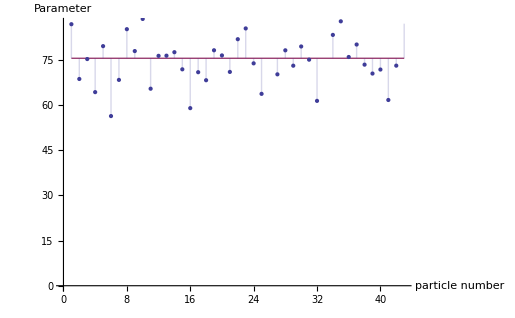

```mathematica
ClearAll["Global'*"]
surfaceImage=-Graphics-;
m=DeleteSmallComponents[DeleteBorderComponents[MorphologicalComponents[ColorNegate[Binarize[surfaceImage]]]]];
m//Colorize
measuresParam=ComponentMeasurements[m,"Area"][[All,2]];
measuresParam=measuresParam*400/3600 (*Scaling*);
meanmeasuresParam=Mean[measuresParam];
combined=MapThread[{#1,#2}&,{Array[#&,Length[measuresParam]],measuresParam}];
combinedZ=combined;
combinedZ[[All,2]]=meanmeasuresParam
ListPlot[{combined,combinedZ},Joined->{False,True},AxesOrigin->{0,0},AxesLabel->{"particle number","Parameter"},Filling->{1->{2}}]
```